```mathematica
Experiment_Condition_Nstep
```

```mathematica
Timing[
ClearAll[dist,xpx,ypy,zpz,orb,Bz,Br,gamma,Bz0,Aθ,CAM,AM,MP,Rd,KE,V,S,F,De,CAM];

(*Parameter list in order to read simuilation data files*)

V[1]={"0","1","2","3"};
V[2]={"5000","10000","50000","100000"};

(*Needed physical parameters*)

clight=2.99792458*10^8;(*Speed of light*)
m=238*1.66053892*10^-27;(*Mass of particle*)
q=34*1.60217657*10^-19;(*Charge of particle*)
R=0.08;(*Solenoid radius*)
l=0.3;(*Solenoid length*)
Bz0=1.7647058823529411;(*Scaling factor for magnetic fields*)
De[1]={5,10,50,100};(*Thin down datas to reduce a calculation time*)

(* Read in data file: put your directory path here *)

Table[orb[i,j]=Import["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Warp_Change_nstep/orbit"<>ToString[V[1][[i]]]<>"_Lz20_nr101_nz3001_Vz3e7_Bz1.0_NStep"<>ToString[V[2][[j]]]<>".dat","Table"],{i,1,4},{j,1,4}];

Aθ[r_,z_]:=NIntegrate[(R^2*r)/(2π)((Sin[θ]*Sin[θ])/(R^2+r^2-2R*r*Cos[θ]))*((z+l/2)/(√((z+l/2)^2+R^2+r^2-2R*r*Cos[θ]))-(z-l/2)/(√((z-l/2)^2+R^2+r^2-2R*r*Cos[θ]))),{θ,0,2π}]/(Bz0);(*Vector potential of thin coil solenoid*)

Table[LENG[i,j]=Length[orb[i,j]],{i,1,4},{j,1,4}];(*Count the lines of each data file*)

(*Make lists of particle orbits*)

Table[x[i,j]=orb[i,j][[All,2]],{i,1,4},{j,1,4}];
Table[y[i,j]=orb[i,j][[All,3]],{i,1,4},{j,1,4}];
Table[z[i,j]=orb[i,j][[All,4]],{i,1,4},{j,1,4}];
Table[vx[i,j]=orb[i,j][[All,5]],{i,1,4},{j,1,4}];
Table[vy[i,j]=orb[i,j][[All,6]],{i,1,4},{j,1,4}];
Table[vz[i,j]=orb[i,j][[All,7]],{i,1,4},{j,1,4}];

(*Lorentz factor gamma and radial amplitude for each simulation step*)

Table[gamma[i,j]=√(1/(1-((vx[i,j]^2+vy[i,j]^2+vz[i,j]^2)/clight^2))),{i,1,4},{j,1,4}];
Table[RS[i,j]=Table[√(x[i,j][[n]]*x[i,j][[n]]+y[i,j][[n]]*y[i,j][[n]]),{n,1,LENG[i,j]}],{i,1,4},{j,1,4}];

(*Not scaled and scaled canonical angular momentum vs z*)

Table[CAM[i,j]=Table[{z[i,j][[n]],10^6*(m*gamma[i,j][[n]]*(x[i,j][[n]]*vy[i,j][[n]]-y[i,j][[n]]*vx[i,j][[n]])+q*Aθ[RS[i,j][[n]],z[i,j][[n]]]*RS[i,j][[n]])/(m*clight)},{n,1,LENG[i,j],De[1][[j]]}],{i,1,4},{j,1,4}];

Table[CAMSCALE[i,j]=Table[{z[i,j][[n]],CAM[i,j][[1+(n-1)/De[1][[j]],2]]/(CAM[i,j][[1,2]])},{n,1,LENG[i,j],De[1][[j]]}],{i,1,4},{j,1,4}];

(*Making lists of simulation step number vs maxmum error amplitude*)

S[1]={5000,10000,50000,100000};
Table[MaxPtN[i,j]={S[1][[j]],Max[CAMSCALE[i,j][[All,2]]]},{i,1,4},{j,1,4}];

]
```

{78.4468,Null}

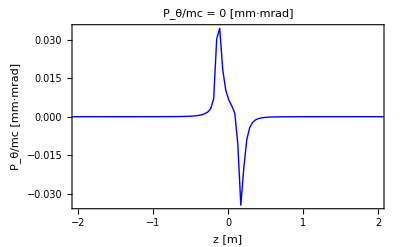

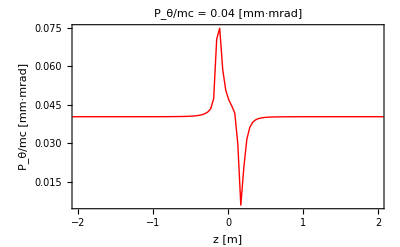

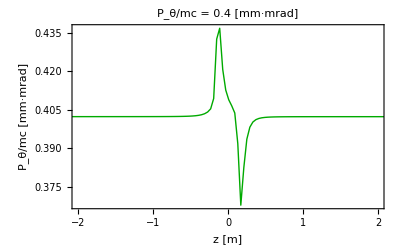

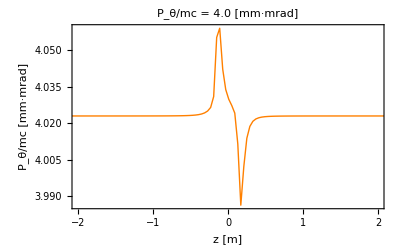

```mathematica
(*P_theta/mc vs z with several simulation step number*)

PT[1]=ListPlot[CAM[1,4],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Blue},PlotLabel->Style["P_θ/mc = 0 [mm·mrad]",17]]
PT[2]=ListPlot[CAM[2,4],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Red},PlotLabel->Style["P_θ/mc = 0.04 [mm·mrad]",17]]
PT[3]=ListPlot[CAM[3,4],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Darker[Green]},PlotLabel->Style["P_θ/mc = 0.4 [mm·mrad]",17]]
PT[4]=ListPlot[CAM[4,4],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/mc [mm·mrad]"},LabelStyle->Directive[18],PlotStyle->{Orange},PlotLabel->Style["P_θ/mc = 4.0 [mm·mrad]",17]]
```

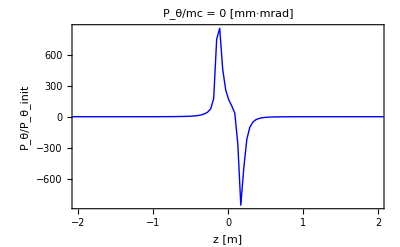

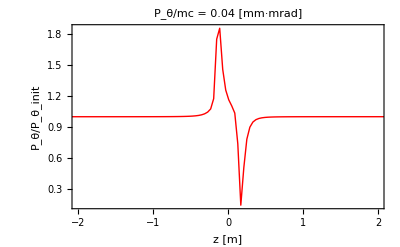

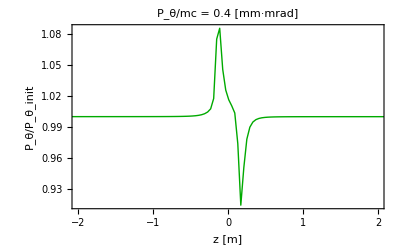

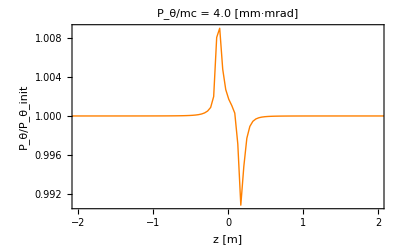

```mathematica
(*Scaled P_theta/mc vs z with several simulation step number*)

PS[1]=ListPlot[CAMSCALE[1,4],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/P_θ_init"},LabelStyle->Directive[18],PlotStyle->{Blue},PlotLabel->Style["P_θ/mc = 0 [mm·mrad]",17]]
PS[2]=ListPlot[CAMSCALE[2,4],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/P_θ_init"},LabelStyle->Directive[18],PlotStyle->{Red},PlotLabel->Style["P_θ/mc = 0.04 [mm·mrad]",17]]
PS[3]=ListPlot[CAMSCALE[3,4],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/P_θ_init"},LabelStyle->Directive[18],PlotStyle->{Darker[Green]},PlotLabel->Style["P_θ/mc = 0.4 [mm·mrad]",17]]
PS[4]=ListPlot[CAMSCALE[4,4],PlotRange->{{-2,2},All},Axes->None,Frame->True,Joined->True,FrameLabel->{"z [m]","P_θ/P_θ_init"},LabelStyle->Directive[18],PlotStyle->{Orange},PlotLabel->Style["P_θ/mc = 4.0 [mm·mrad]",17]]
```

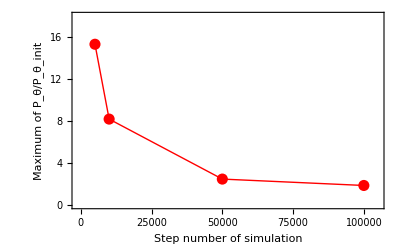

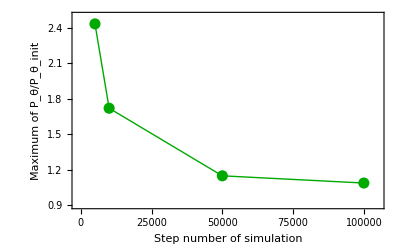

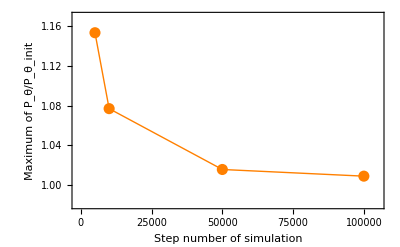

```mathematica
(*Maxmum error amplitude vs simulation step number*)

SPt[1]=Show[
ListPlot[Table[MaxPtN[2,j],{j,1,4}],PlotStyle->{PointSize[0.02],Red},Axes->None,Frame->True,Joined->True,FrameLabel->{"Step number of simulation","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[15],PlotRange->{{-1000,105000},{0,18}}],
ListPlot[Table[MaxPtN[2,j],{j,1,4}],PlotStyle->{PointSize[0.02],Red},Axes->None,Frame->True,FrameLabel->{"z [m]","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[18]]
]

SPt[2]=Show[
ListPlot[Table[MaxPtN[3,j],{j,1,4}],PlotStyle->{PointSize[0.02],Darker[Green]},Axes->None,Frame->True,Joined->True,FrameLabel->{"Step number of simulation","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[15],PlotRange->{{-1000,105000},{0.9,2.5}}],
ListPlot[Table[MaxPtN[3,j],{j,1,4}],PlotStyle->{PointSize[0.02],Darker[Green]},Axes->None,Frame->True,FrameLabel->{"z [m]","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[18]]
]

SPt[3]=Show[
ListPlot[Table[MaxPtN[4,j],{j,1,4}],PlotStyle->{PointSize[0.02],Orange},Axes->None,Frame->True,Joined->True,FrameLabel->{"Step number of simulation","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[15],PlotRange->{{-1000,105000},{0.98,1.17}}],
ListPlot[Table[MaxPtN[4,j],{j,1,4}],PlotStyle->{PointSize[0.02],Orange},Axes->None,Frame->True,FrameLabel->{"z [m]","Maximum of P_θ/P_θ_init"},LabelStyle->Directive[18]]
]
```

```mathematica
(*Export graphic data to the directory on your computer:you have to specify the directory where you want to export*)

Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_Norm_emit_4e-8.eps",SPt[1],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_Norm_emit_4e-7.eps",SPt[2],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_Norm_emit_4e-6.eps",SPt[3],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_Pthe_time_evol_0.eps",PT[1],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_Pthe_time_evol_4e-8.eps",PT[2],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_Pthe_time_evol_4e-7.eps",PT[3],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_Pthe_time_evol_4e-6.eps",PT[4],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_PtheN_time_evol_0.eps",PS[1],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_PtheN_time_evol_4e-8.eps",PS[2],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_PtheN_time_evol_4e-7.eps",PS[3],"EPS"];
Export["/Users/oosakikazuya/Dropbox/warp_nonlinear_conf/Fig_change_steps/Nstep_PtheN_time_evol_4e-6.eps",PS[4],"EPS"];
```